### Hierarchical representation of Brownian increments

Given an interval [0,1], we are trying to represent increments W_(t_(i+1))-W_t_i, t_i=i 2^-m, i=0,...,2^m, by means of the hierarchical representation in terms of Haar basis. We start with defining the Schauder functions on [0,1].

#### Schauder functions

Functions are defined for n≥1and 1≤j≤2^n-1.

```mathematica
F[n_,j_,t_]:=Piecewise[{{2^((n-1)/2) (t-(j-1)2^(-n)),(j-1)2^(-n)≤t≤j 2^(-n)},{2^((n-1)/2) ((j+1)2^(-n)-t),j 2^(-n)<t≤(j+1)2^(-n)}},0]
```

Plot Schauder functions.

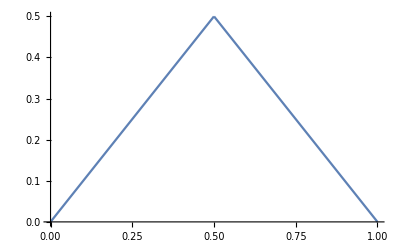

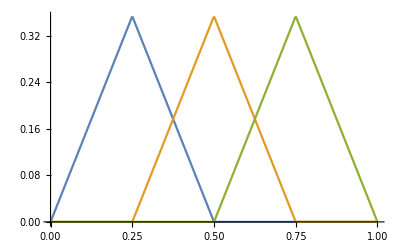

```mathematica
Plot[F[1,1,t],{t,0,1}]
Plot[{F[2,1,t],F[2,2,t],F[2,3,t]},{t,0,1}]
```

We see the problem: the second “tent” at level 2 is not supposed to be independent of the tent at level 1: We should only include those level n Schauder functions such that the barycenter of the support is not already contained in one of the previous levels, i.e., such that j is odd.

#### Construction of the Brownian motion

Define the Brownian motion up to order m in terms of standard normals Z_0 and Z_(n,j).

```mathematica
(*W[m_,t_]:=Subscript[Z, 0] t + Sum[Sum[Z[n,j] F[n,j,t],{j,1,2^n-1}],{n,1,m}]*)
```

```mathematica
W[5,1/2]
```

Z_0/2+1/2 Z[1,1]

As we saw later, this definition is incorrect. See below for the correct one.

#### Construction of the increments on scale m

Consider the increments at scale m.

```mathematica
dW[m_,i_]:=W[m,(i+1)2^(-m)]-W[m,i 2^(-m)]
```

```mathematica
dW[5,3]
dW[8,5]
```

Z_0/32+1/32 Z[1,1]+Z[2,1]/(16 √2)+1/16 Z[3,1]-Z[4,1]/(8 √2)-1/8 Z[5,3]

Z_0/256+1/256 Z[1,1]+Z[2,1]/(128 √2)+1/128 Z[3,1]+Z[4,1]/(64 √2)+1/64 Z[5,1]-Z[6,1]/(32 √2)+1/32 Z[7,3]-Z[8,5]/(16 √2)

Conjecture: increments at level m have m+1 terms appearing. (Not 2m+1 like in my own formula.)

#### Check the distribution

Read out the coefficients to check for the distribution of the resulting Brownian increment.

```mathematica
dWlist[m_,i_]:=Prepend[Flatten[Table[Table[Coefficient[dW[m,i],Z[n,j]],{j,1,2^n-1}],{n,1,m}]],Coefficient[dW[m,i],Subscript[Z, 0]]]
```

```mathematica
dWlist[5,3]
```

{1/32,1/32,1/(16 √2),0,0,1/16,0,0,0,0,0,0,-1/(8 √2),1/(8 √2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Compute the variance of the ith increment at scale m.

```mathematica
dWvar[m_,i_]:=dWlist[m,i].dWlist[m,i]
```

Compare with the true value 2^-m.

```mathematica
dWvar[5,3]
2^(-5)
```

7/128

1/32

Now we also compute the covariance.

```mathematica
dWcovar[m_,i_,j_]:=dWlist[m,i].dWlist[m,j]
```

Conclusion: something seems wrong with the formula.

### Alternative construction including odd j only.

For details, see the above construction. We sum over al j which are odd.

```mathematica
W[m_,t_]:=Subscript[Z, 0] t + Sum[Sum[Boole[OddQ[j]]Z[n,j] F[n,j,t],{j,1,2^n-1}],{n,1,m}]
```

Test at t=1, t=1/2, where only Z_0 and Z_0,Z_(1,1) should be active.

```mathematica
W[5,1]
W[5,1/2]
```

Z_0

Z_0/2+1/2 Z[1,1]

All other definitions remain unchanged. Let us check the results then.

```mathematica
dWvar[5,3]
2^(-5)
```

1/32

1/32

This works! We also need to check that the different increments are independent. Provided this is true, everything is correct!

```mathematica
dWcovar[5,3,4]
```

0

Try later terms.

```mathematica
dWvar[5,2^5-1]
2^(-5)
```

1/32

1/32

Still seems to work, but let us try it more systematically.

```mathematica
dWvarList[m_]:=Table[dWvar[m,i],{i,0,2^m-1}]
```

```mathematica
dWvarList[5]
```

{1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32,1/32}

```mathematica
dWvarList[6]
```

{1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64,1/64}

#### Compare with exact formula for differences

Define the exact formula of the differences at scale m.

```mathematica
ι[i_,n_,m_]:=Boole[EvenQ[Floor[i 2^(n-m)]]]
```

```mathematica
dWexact[m_,i_]:=Subscript[Z, 0] 2^(-m)+Sum[2^((n-2m-1)/2) (-1)^(ι[i,n,m]+1) Z[n,Floor[i 2^(n-m)]+ι[i,n,m]],{n,1,m}]
```

Compare the results.

```mathematica
dW[5,3]
dWexact[5,3]
```

Z_0/32+1/32 Z[1,1]+Z[2,1]/(16 √2)+1/16 Z[3,1]-Z[4,1]/(8 √2)-1/8 Z[5,3]

Z_0/32+1/32 Z[1,1]+Z[2,1]/(16 √2)+1/16 Z[3,1]-Z[4,1]/(8 √2)-1/8 Z[5,3]

```mathematica
dW[8,2^8-1]
dWexact[8,2^8-1]
```

Z_0/256+1/256 Z[1,1]+Z[2,1]/(128 √2)+1/128 Z[3,1]+Z[4,1]/(64 √2)+1/64 Z[5,1]+Z[6,1]/(32 √2)-1/32 Z[7,1]-Z[8,3]/(16 √2)

Z_0/256+1/256 Z[1,1]+Z[2,1]/(128 √2)+1/128 Z[3,1]+Z[4,1]/(64 √2)+1/64 Z[5,1]+Z[6,1]/(32 √2)-1/32 Z[7,1]-Z[8,3]/(16 √2)

This finally seems to work!

#### Miscellaneous computations

```mathematica
ind[n_,j_]:=2^(n-1)+(j-1)/2+1
```

```mathematica
ind[1,1]
ind[2,1]
ind[2,3]
Table[ind[3,j],{j,1,7,2}]
Table[ind[4,j],{j,1,16,2}]
```

2

3

4

{5,6,7,8}

{9,10,11,12,13,14,15,16}